## Etymology of Trig Functions

### Straight lines

#### point - slope form

```mathematica
ptsl[m_,p_,x_]:=m x+ p[[2]]-m p[[1]]
```

```mathematica
ptsl[m_,p_,x_]:=m (x-p[[1]])+ p[[2]]//Simplify
```

```mathematica
ptsl[3,{1,2},x]
```

-1+3 x

#### two-point form

```mathematica
tpl[p_,q_,x_]:=(p[[2]]-q[[2]])/(p[[1]]-q[[1]])(x-p[[1]])+p[[2]]//Simplify
```

```mathematica
tpl[{1,2},{0,-1},x]
```

-1+3 x

```mathematica
tpl[{0,-1},{1,2},x]
```

-1+3 x

```mathematica
tpl[{1,4},{5,2},x]
```

(9-x)/2

### Secant lines

```mathematica
(1.5)^2-1/5
```

2.05

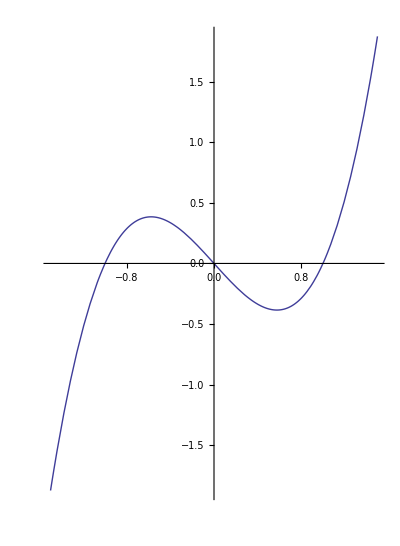

```mathematica
Plot[x^3-x,{x,-1.5,1.5},AspectRatio->4.1/3]
```

```mathematica
cu[x_]:=x^3-x;cud[x_]:=cu'[x]
```

```mathematica
tpl[{a,cu[a]},{b,cu[b]},x]
```

(-1+b^2) x+a^2 (-b+x)+a b (-b+x)

```mathematica
Manipulate[
Plot[
{cu[x],
tpl[{a,cu[a]},{b,cu[b]},x]
},
{x,-1.5,1.5},PlotRange->{{-1.5,1.5},{-4.2,4.2}},PlotStyle->{Blue,Red},
AspectRatio->4.1/3
],
{{a,-1},-1.5,1.5,Appearance->"Labeled"},{{b,.5},-1.5,1.5,Appearance->"Labeled"},
SaveDefinitions->True
]
```

```mathematica
ptsl[cud[1],{1,cu[1]},x]
```

2 (-1+x)

```mathematica
Manipulate[
Plot[
{cu[x],
If[
a==b,
ptsl[cud[a],{a,cu[a]},x],
tpl[{a,cu[a]},{b,cu[b]},x]
]
},
{x,-1.5,1.5},PlotRange->{{-1.5,1.5},{-2.2,2.2}},PlotStyle->{Blue,Red},
AspectRatio->4.4/3
],
{{a,-1},-1.5,1.5},{{b,.5},-1.5,1.5},
SaveDefinitions->True
]
```

```mathematica
Manipulate[
Show[
Plot[
{cu[x],
If[
a==b,
ptsl[cud[a],{a,cu[a]},x],
tpl[{a,cu[a]},{b,cu[b]},x]
]
},
{x,-1.5,1.5},PlotRange->{{-1.5,1.5},{-2.2,2.2}},PlotStyle->{Blue,Red},
AspectRatio->4.4/3
],
Graphics[
{Black,
PointSize[.02],
Point[{a,cu[a]}],
Point[{b,cu[b]}]
}
]
],
{{a,-1},-1.5,1.5},{{b,.5},-1.5,1.5},
SaveDefinitions->True
]
```

### Tangent lines

```mathematica
Manipulate[
Show[
Plot[
{cu[x],
ptsl[cud[a],{a,cu[a]},x]
},
{x,-1.5,1.5},PlotRange->{{-1.5,1.5},{-2.2,2.2}},PlotStyle->{Blue,Red},
AspectRatio->4.4/3
],
Graphics[
{Black,
PointSize[.02],
Point[{a,cu[a]}],
}
]
],
{{a,-1},-1.5,1.5},
SaveDefinitions->True
]
```